1.00075

-0.8365

0.9422

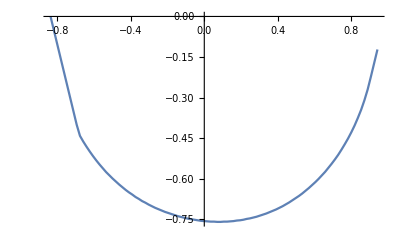

xvec.csv

critomvec.csv

```mathematica
Clear["Global`*"];
sigma=2;
a=-0.1;
b=0.1;
alpha=0.5;

qmin = 0.001;
qmax = 4.0;
numq = 101;
qvec = Table[myq, {myq, qmin, qmax, (qmax-qmin)/(numq-1)}];

fvec = Table[100, {myq, qmin, qmax, (qmax-qmin)/(numq-1)}];


Monitor[Do[


q = qvec[[i]];

effinf = 4Sqrt[q sigma^2];
myq= NIntegrate[(((b-1/alpha)+ Sqrt[(b-1/alpha)^2+ 4 a (1+ (1-alpha)/alpha eta)])/(2a))^2Exp[-eta^2/(2 sigma^2 q)]/Sqrt[2Pi sigma^2 q],{eta,-2, 2}]+ 1/2  Erfc[√2 √(1/(q sigma^2))](((b-1/alpha)+ Sqrt[(b-1/alpha)^2+ 4 a (1+ 2(1-alpha)/alpha )])/(2a))^2 + 1/2  Erfc[√2 √(1/(q sigma^2))](((b-1/alpha)+ Sqrt[(b-1/alpha)^2+ 4 a (1- 2(1-alpha)/alpha )])/(2a))^2;
fvec[[i]]=(myq-q)^2;



,{i, 1, numq}];,i];

nearest = Min[Abs[fvec]];
pos = Position[Abs[fvec], nearest][[1,1]];
q = qvec[[pos]]

xmin =-1.0;
xmax = -0.5;
numx = 1001;
xvec = Table[x, {x, xmin, xmax, (xmax-xmin)/(numx -1)}];
fvec = Table[100, {x, xmin, xmax, (xmax-xmin)/(numx -1)}];

Monitor[Do[
omx  = xvec[[j]];





fvec[[j]]= NIntegrate[Exp[-eta^2/(2 sigma^2 q)]/Sqrt[2Pi sigma^2 q](omx^2)sigma^2(1-alpha)^2/Abs[(omx)^2 + 2 alpha a (((b-1/alpha)+ Sqrt[(b-1/alpha)^2+ 4 a (1+ (1-alpha)/alpha eta)])/(2a))(omx)- alpha b]^2,{eta, -2, 2}] ;





,{j, 1, numx}];,j];
nearest = Nearest[fvec,1][[1]];
pos = Position[fvec, nearest][[1,1]];
xminc = xvec[[pos]]


xmin =0.5;
xmax = 1.1;
numx = 1001;
xvec = Table[x, {x, xmin, xmax, (xmax-xmin)/(numx -1)}];
fvec = Table[100, {x, xmin, xmax, (xmax-xmin)/(numx -1)}];

Monitor[Do[
omx  = xvec[[j]];




fvec[[j]]= NIntegrate[Exp[-eta^2/(2 sigma^2 q)]/Sqrt[2Pi sigma^2 q](omx^2)sigma^2(1-alpha)^2/Abs[(omx)^2 + 2 alpha a (((b-1/alpha)+ Sqrt[(b-1/alpha)^2+ 4 a (1+ (1-alpha)/alpha eta)])/(2a))(omx)- alpha b]^2,{eta, -2, 2}] ;





,{j, 1, numx}];,j];
nearest = Nearest[fvec,1][[1]];
pos = Position[fvec, nearest][[1,1]];
xmaxc = xvec[[pos]]


xmin =xminc;
xmax = xmaxc;
numx = 101;
xvec = Table[x, {x, xmin, xmax, (xmax-xmin)/(numx -1)}];


critomvec = Table[x,{x, xmin, xmax, (xmax-xmin)/(numx -1)}];


ymin = 0.0;
ymax = 1;
numy = 101;
yvec = Table[y, {y, ymin, ymax, (ymax-ymin)/(numy -1)}];

Monitor[Do[
omx  = xvec[[j]];

fvec = Table[100, {y, ymin, ymax, (ymax-ymin)/(numy -1)}];

Monitor[Do[


omy  = yvec[[i]];

fvec[[i]]= NIntegrate[Exp[-eta^2/(2 sigma^2 q)]/Sqrt[2Pi sigma^2 q](omx^2 + omy^2)sigma^2(1-alpha)^2/Abs[(omx+I omy)^2 + 2 alpha a (((b-1/alpha)+ Sqrt[(b-1/alpha)^2+ 4 a (1+ (1-alpha)/alpha eta)])/(2a))(omx+I omy)- alpha b]^2,{eta, -2, 2}] ;




,{i, 1, numy}];,i];
nearest = Nearest[fvec,1][[1]];
pos = Position[fvec, nearest][[1,1]];
critomvec[[j]] = yvec[[pos]];

ymin = yvec[[pos]]-0.05;
ymax = yvec[[pos]]+0.05;
numy = 101;
yvec = Table[y, {y, ymin, ymax, (ymax-ymin)/(numy -1)}];
,{j, 1, numx}];,j];

ListLinePlot[Transpose[{xvec, critomvec}]]



SetDirectory[NotebookDirectory[]];
Export["xvec.csv", xvec]
Export["critomvec.csv", critomvec]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["xvec.csv", xvec]
Export["critomvec.csv", critomvec]
```

xvec.csv

critomvec.csv

```mathematica
fvec
```

{20.7005,2.11124,0.15162,0.0306732,0.0100624,0.00432567,0.00220873,0.0012707,0.000798147,0.000536381,0.000380409,0.000281963,0.000216873,0.000172176,0.000140513,0.000117503,0.000100435,0.00008757,0.0000777628,0.0000702402,0.0000644709,0.0000600854,0.000056826,0.0000545152,0.0000530353,0.0000523164,0.0000523291,0.000053082,0.0000546236,0.0000570476,0.0000605044,0.0000652198,0.0000715258,0.0000799096,0.0000910942,0.000106174,0.000126847,0.000155838,0.000197694,0.000260355,0.000358503,0.000521206,0.000811127,0.00137888,0.00264243,0.00601802,0.0179705,0.0870669,1.18901,11.4404,0.326521,0.0322733,0.00694015,0.00219773,0.00087415,0.000403936,0.000207563,0.000115451,0.0000682892,0.0000424293,0.0000274462,0.0000183621,0.000012641,8.91943×10^-6,6.42992×10^-6,4.72356×10^-6,3.52864×10^-6,2.67578×10^-6,2.0566×10^-6,1.60013×10^-6,1.25891×10^-6,1.00058×10^-6,8.02732×10^-7,6.49587×10^-7,5.29874×10^-7,4.35441×10^-7,3.60318×10^-7,3.00085×10^-7,2.51435×10^-7,2.11869×10^-7,1.79482×10^-7,1.52811×10^-7,1.30721×10^-7,1.12326×10^-7,9.6929×10^-8,8.39792×10^-8,7.30374×10^-8,6.37518×10^-8,5.5839×10^-8,4.90691×10^-8,4.32554×10^-8,3.82446×10^-8,3.3911×10^-8,3.01508×10^-8,2.68777×10^-8,2.402×10^-8,2.15178×10^-8,1.93207×10^-8,1.73864×10^-8,1.56791×10^-8,1.41683×10^-8}